# 2. izpit – Mathematica

## Računalniški praktikum 2023/24

Študijske smeri: Aplikativna fizika, Praktična matematika

## Podatki o študentu

Vpišite svoje podatke

Ime:

Priimek:

Vpisna številka:

## Navodila

Čas reševanja za celoten izpit je 120 minut.
V tem delu izpita so tri naloge, ki so skupaj vredne 30 točk od 100 možnih na izpitu.
Vsako nalogo rešujte v svojem razdelku.
Dovoljeno je uporabljati dokumentacijo o Mathematici in gradivo iz vaj.
Vsakršna komunikacija je prepovedana.

## 1. naloga [5 točk]

Preverite, da velja enakost . 
 pomeni prodkut členov, tako kot  pomeni vsota členov. Pomagajte si z ukazoma Product in Simplify.

```mathematica
funkcija1=product[1-(1/k^2),{k,2,n}]
funkcija2=1/2*(1+(1/n))
Simplify[funkcija1,funkcija2]
```

product[1-1/k^2,{k,2,n}]

1/2 (1+1/n)

product[1-1/k^2,{k,2,n}]

## 2. naloga [15 točk]

1. (5 točk) Definirajte funkcijo f s predpisom f(x)=.
2. (5 točk) Izračunajte odvod funkcije f'(x) in njene stacionarne točke (ničle odvoda).
3. (5 točk) Narišite grafa f in f' na istem koordinatnem sistemu na intervalu [-3,3].

```mathematica
ClearAll[x]
```

```mathematica
f[x_]:=((x^3)-(2*(x^2))+1)/(x^2-1)
f'[x]
D[f[x],x]
x/.Solve[D[f[x],x]==0]
ParametricPlot[f[x],f'[x],{x,-3,3}]
```

(-4 x+3 x^2)/(-1+x^2)-(2 x (1-2 x^2+x^3))/((-1+x^2)^2)

(-4 x+3 x^2)/(-1+x^2)-(2 x (1-2 x^2+x^3))/((-1+x^2)^2)

{-2,0}

ParametricPlot::pllim: Range specification f'[x] is not of the form {x, xmin, xmax}.

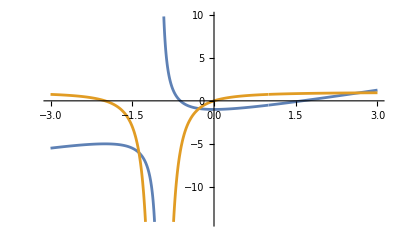

SetDelayed::write: Tag D in D[(1-2 x^2+x^3)/(-1+x^2)] is Protected.

```mathematica
Plot[{f[x],f'[x]},{x,-3,3}]
```

## 3. naloga [10 točk]

1. (5 točk) S pomočjo funkcije Table definirajte funkcijo koeficienti, ki sprejme parameter n in vrne seznam binomskih koeficientov .
Primer: koeficienti[5] naj vrne {1,5,10,10,5,1}. Uporabite lahko funkcijo Binomial.
2. (5 točk) Nekatere matematike zanima (ker je to povezano z generiranjem alternirajočih grup), kateri binomski koeficienti so deljivi z določenimi velikimi praštevili. 
Izpišite seznam vseh binomskih koeficientov števila 31416, ki so deljivi s praštevilom 7853. Ta izračun bo nekaj časa trajal; za začetek lahko preizkusite število 210 in praštevilo 199. Lahko si pomagate s pomožno funkcijo (lahko uporabite funkcijo Divisible).

```mathematica
ClearAll[n,k]
```

```mathematica
koeficienti[n_]:=Table[Binomial[n,k],{k,0,n}]
```

SetDelayed::write: Tag Table in Table[Binomial[n,k],{k,0,n}][n_] is Protected.

$Failed

```mathematica
koeficienti[5]
```